```mathematica
ClearAll["Global*'"]
```

```mathematica
Tlist={0.001, 0.00158489 ,0.00251189 ,0.00398107 ,0.00630957 ,0.01, 0.01584893, 0.02511886, 0.03981072, 0.06309573 ,0.1,0.11, 0.12 ,0.13};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.00100000,0.00158489,0.00251189,0.00398107,0.00630957,0.01000000,0.01584893,0.02511886,0.03981072,0.06309573,0.10000000,0.11000000,0.12000000,0.13000000}

```mathematica
plist={3.70, 3.72 ,3.74 ,3.76 ,3.78, 3.80,3.82,3.84,3.86,3.88,3.90};
pstring=ToString[NumberForm[#,{5,3},ExponentFunction->(Null&)]]&/@plist
```

{3.700,3.720,3.740,3.760,3.780,3.800,3.820,3.840,3.860,3.880,3.900}

```mathematica
datasets=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/preliminary_N900_p",pstring[[p]],"_T",Tstring[[T]],"_time5000000.nc"],"Data"],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
Import[""]
```

```mathematica
data=Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/preliminary_N900_p3.700_T0.00001000_time5000000.nc","Datasets"]
```

{/BoxMatrix,/d2Edgammadgamma,/energy,/sigma}

```mathematica
|
```

```mathematica
area=datasets[[1,1]][[1,1]][[4]]*datasets[[1,1]][[1,1]][[4]];
```

```mathematica
datasets[[6,9]][[4,4999]][[1]]
```

-0.00200536

```mathematica
Gp=Table[Table[Table[datasets[[p,T]][[2,i]][[1]],{i,10001,50000}],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
Sigmap=Table[Table[Table[datasets[[p,T]][[4,i]][[1]]*area,{i,10001,50000}],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
varsig=Table[Table[Variance[Sigmap[[p,T]]],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
meanG=Table[Table[Mean[Gp[[p,T]]],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
G=Table[Table[1/area*(meanG[[p,i]]-varsig[[p,i]]/Tlist[[i]]),{i,Length[Tlist]}],{p,Length[pstring]}]
```

{{0.153196,0.173576,0.0759961,-0.493009,0.132028,0.104641,0.208159,0.0296451,0.0778676,0.157693,-2.13967×10^6,0.275118,-2830.35,-4580.55},{0.127199,0.0659617,-0.00523916,0.0804926,0.125539,0.160319,-0.0514819,0.0467962,0.0846578,0.165561,-0.0428393,-173.978,-204.554,-105.145},{0.0713412,-0.0903415,0.0426996,-0.210705,0.102778,0.132254,0.0261373,0.0527381,0.0986215,0.155887,0.26415,-0.331877,0.0235786,-27.5839},{0.0107573,0.0104733,0.0319418,0.0495629,0.0638095,0.00784141,0.0213052,0.0596623,0.106482,0.173086,0.26043,-0.684861,-0.543682,-14.6764},{0.00197621,0.0101628,0.0239398,0.019175,0.00784663,0.0110231,0.0306252,0.070368,0.107354,0.128883,-0.431002,-18.8056,-1161.16,-80017.7},{0.0036069,0.00703719,0.0001226,0.00331456,0.00737432,0.022223,0.0424961,0.0695381,0.109314,0.176227,-3138.55,-690.39,-2.75596,-12.9744},{0.00197454,-0.00148564,0.00434201,0.00775038,0.014402,0.0279236,0.043999,0.0719338,0.1136,0.177828,-5.63535,-40.3443,-45.277,-34.8436},{0.00256409,0.00405813,0.00859385,0.0104017,0.017495,0.0270043,0.0485023,0.0776292,0.121215,0.174081,-5.54635,-963.611,-203.024,-77.5268},{0.00211193,0.00823601,0.0124221,0.0162074,0.0258295,0.0365396,0.0482157,0.0776253,0.124762,-11.5015,-1.19405×10^6,-46283.2,-2.79724,-29040.3},{0.00630416,0.00556908,0.0115341,0.0183535,0.0279186,0.0394071,0.052376,0.0802879,0.12233,0.163547,-1476.66,-522.28,-8.3857×10^7,-2190.31},{0.00417844,0.00795937,0.0106376,0.0191431,0.0245016,0.0367088,0.0561485,0.0367291,0.11989,-2.70332,-38477.7,-863.002,-1805.46,-27638.4}}

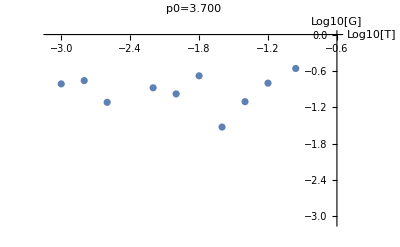
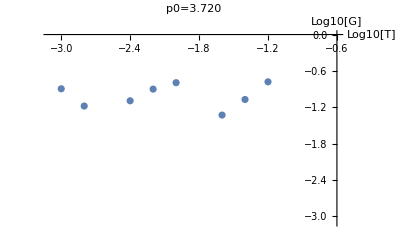
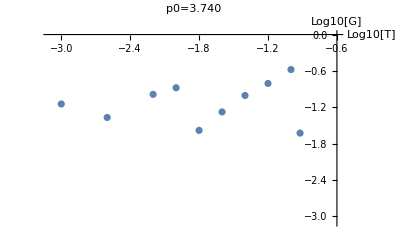
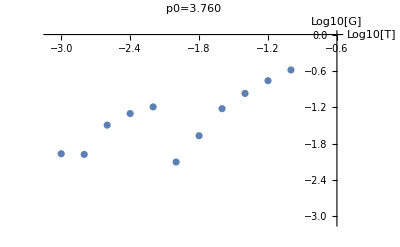
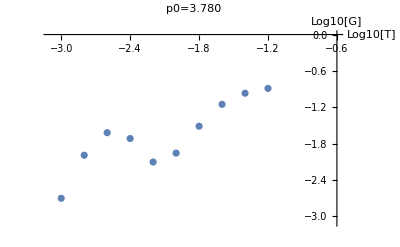
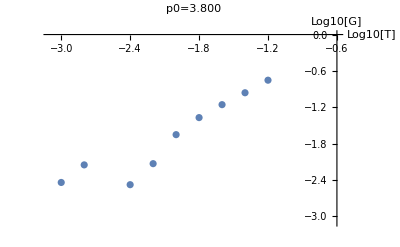
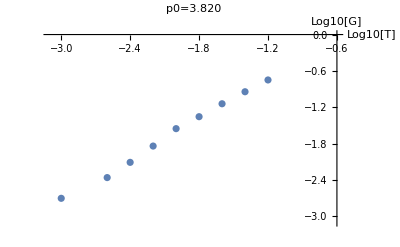
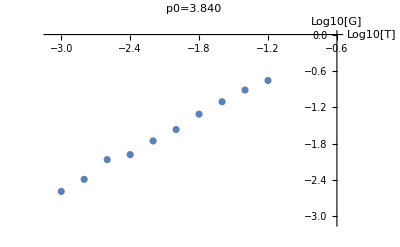

```mathematica
Table[ListPlot[Table[{Log10[Tlist[[i]]],Log10[G[[j,i]]]},{i,Length[Tlist]}],AxesLabel->{"Log10[T]","Log10[G]"},PlotRange->{{-3.1,-0.6},{-3.1,0}},ImageSize->400,PlotLabel->StringJoin["p0=",pstring[[j]]]],{j,Length[plist]}]
```

```mathematica
loglog=Table[Table[{Log10[Tlist[[i]]],Log10[G[[j,i]]]},{i,Length[Tlist]}],{j,Length[plist]}];
```

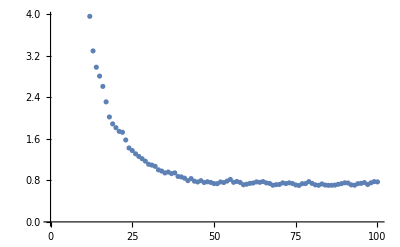

```mathematica
ListPlot[Table[datasets[[6,1]][[3,i]][[1]],{i,1,100}]]
```

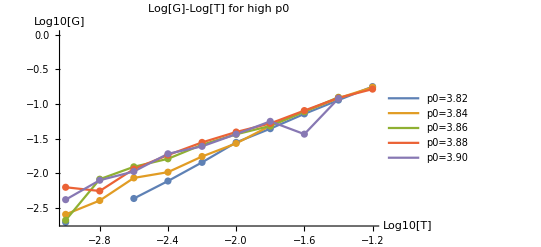

```mathematica
colors=ColorData[97,"ColorList"]; 
ListPlot[loglog[[7;;11]],Joined->True,Mesh->All,PlotLegends->{"p0=3.82","p0=3.84","p0=3.86","p0=3.88","p0=3.90"},AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->400,PlotLabel->"Log[G]-Log[T] for high p0"]
```

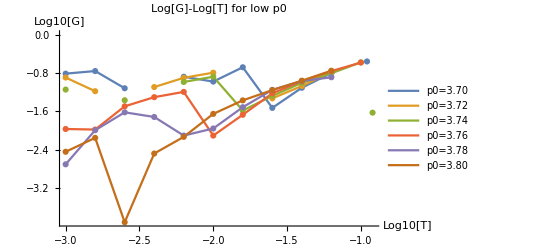

```mathematica
colors=ColorData[97,"ColorList"]; 
ListPlot[loglog[[1;;6]],Joined->True,Mesh->All,PlotLegends->{"p0=3.70","p0=3.72","p0=3.74","p0=3.76","p0=3.78","p0=3.80"},AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->400,PlotLabel->"Log[G]-Log[T] for low p0"]
```